```mathematica
s={Cos[u]Sin[v],Sin[u]Sin[v],Cos[v]};
ParametricPlot3D[s,{u,0,2π},{v,0,π}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[s,{u,0,2 π},{v,0,π},MeshShading->{{Opacity[0]},{Magenta}},ImageSize->Large,PlotPoints->80,MeshFunctions->{Cos[5#4]Sin[#5]+Cos[5#5]&},Mesh->6]
```

-Graphics3D-

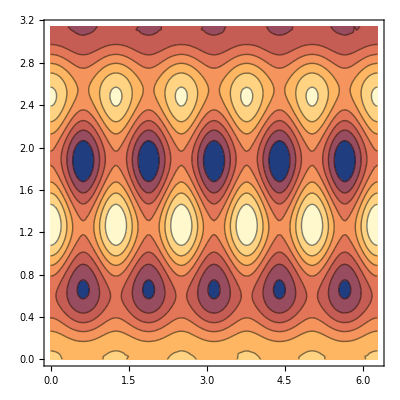

```mathematica
ContourPlot[Cos[5u]Sin[v]+Cos[5v],{u,0,2π},{v,0,π}]
```

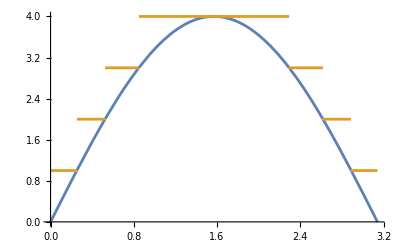

```mathematica
Plot[{4 Sin[t],Ceiling[4 Sin[t]]},{t,0,π}]
```

```mathematica
p=Table[s,{u,0,2π,π/3},{v,0,π,π/4}];
Show[ParametricPlot3D[s,{u,0,2π},{v,0,π},PlotStyle->{Opacity[0.5]}],ListPointPlot3D[p,PlotStyle->{PointSize[Large]}]]
```

-Graphics3D-

```mathematica
ContourPlot[Cos[5u]Sin[v]+Cos[5v],{u,0,2π},{v,0,π}]
```

-Graphics-

```mathematica
ParametricPlot3D[s,{u,0,2 π},{v,0,π},ImageSize->Large,PlotPoints->50,RegionFunction->(Norm[{#1,#2,#3}-s/.{u->Round[#4,(2π)/7],v->Round[#5,π/4]}]>0.2&)]
```

-Graphics3D-

```mathematica
ParametricPlot3D[s,{u,0,2 π},{v,0,π},ImageSize->Large,PlotPoints->3,RegionFunction->(Norm[{#1,#2,#3}-s/.{u->Round[#4,(2π)/7],v->Round[#5,π/4]}]>0.1+0.25Sin[Round[#5,π/4]]&)]
```

-Graphics3D-

```mathematica
ClearAll[s]
```

```mathematica
s[u_,v_]:={Cos[u] Sin[v],Sin[u] Sin[v],Cos[v]}
rf[x_,y_,z_,u_,v_]:=Block[{p={x,y,z}, c=s[Round[u,(2 π)/7],Round[v,π/4]],θ},
θ=If[p==c||c=={0,0,1}||c=={0,0,-1},0,VectorAngle[{0,0,1}×c,p-c]];Norm[p-c]>(0.1+0.1 Sin[Round[v,π/4]]) (1+0.7Sin[3θ])(*;θ*)]

Table[rf@@{Cos[u] Sin[v],Sin[u] Sin[v],Cos[v],u,v},{u,0,2π,0.1π},{v,0,π,0.1π}]
```

{{False,True,True,True,True,False,True,True,True,True,False},{False,True,False,False,True,True,True,False,False,True,False},{False,True,False,False,True,True,True,False,False,True,False},{False,True,True,True,True,False,True,True,True,True,False},{False,True,True,True,True,True,True,True,True,True,False},{False,True,False,False,True,False,True,False,False,True,False},{False,True,True,True,True,False,True,True,True,True,False},{False,True,True,True,True,True,True,True,True,True,False},{False,True,True,False,True,False,True,False,True,True,False},{False,True,True,False,True,False,True,False,True,True,False},{False,True,True,True,True,True,True,True,True,True,False},{False,True,True,False,True,False,True,False,True,True,False},{False,True,True,False,True,False,True,False,True,True,False},{False,True,True,True,True,True,True,True,True,True,False},{False,True,True,True,True,False,True,True,True,True,False},{False,True,False,False,True,False,True,False,False,True,False},{False,True,True,True,True,True,True,True,True,True,False},{False,True,True,True,True,False,True,True,True,True,False},{False,True,False,False,True,True,True,False,False,True,False},{False,True,False,False,True,True,True,False,False,True,False},{False,True,True,True,True,False,True,True,True,True,False}}

```mathematica
ParametricPlot3D[s[u,v],{u,0,2 π},{v,0,π},ImageSize->Large,PlotPoints->50,RegionFunction->rf]
```

-Graphics3D-

```mathematica
pts=SpherePoints[81];
rf[x_,y_,z_,u_,v_]:=Min[Norm[#-{x,y,z}]&/@pts]>0.12
ParametricPlot3D[s,{u,0,2 π},{v,0,π},ImageSize->Large,PlotPoints->150,RegionFunction->rf,PlotStyle->MaterialShading[{"Copper",Magenta}],Mesh->None,Lighting->"ThreePoint"]
```

-Graphics3D-

```mathematica
pts=SpherePoints[50];
f[x_]:=0.3Sin[x]+0.7
rf[s_]:=f[Min[Norm[#-s]&/@pts]]
ParametricPlot3D[s rf@s,{u,0,2 π},{v,0,π},ImageSize->Large,PlotPoints->150,PlotStyle->MaterialShading[{"Copper",Magenta}],Mesh->None,Lighting->"ThreePoint"]
```

-Graphics3D-